## Spherically symmetric case (1+1D nonlinear PDE)

As in the draft eq. (4.61), I write ∂lnH/∂lna as

```mathematica
dlnHdlna = -(Ωm + (1+3w)(1-Ωm)Exp[-3w lna])/(2Ωm + 2(1-Ωm)Exp[-3w lna]);
```

As an example I will put “nice” numbers, Ωm = 3/10 and w = -5/6. We can solve the time evolution of the linear gravitational potential ψ:

```mathematica
DSolve[(ψ''[lna] +(3+dlnHdlna)ψ'[lna]+(2-(3Ωm)/(2Ωm + 2(1-Ωm)Exp[-3w lna])+dlnHdlna)ψ[lna]== 0)/.Ωm-> 3/10/.w-> -5/6,ψ[lna], lna]
```

{{ψ[lna]→C[1] Hypergeometric2F1[2/5,11/10,2,-7/3 ⅇ^(5 lna/2)]+C[2] MeijerG[{{},{-1/10,3/5}},{{-1,0},{}},-7/3 ⅇ^(5 lna/2)]}}

The first solution is the relevant one (it becomes constant as lna -> -∞):

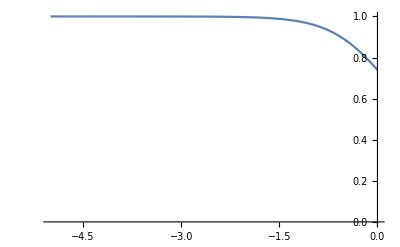

```mathematica
Plot[Hypergeometric2F1[2/5,11/10,2,-7/3 ⅇ^(5 lna/2)],{lna,-5,0},PlotRange->{0,1}]
```

We now need to choose the radial profile of ψ. As is well known, every spherically symmetric function can be expanded in terms of j_0(k r). Let us consider a single spherical wave mode with wave number k. Note that in the following k and r will use units of H_0 so that everything is dimensionless.

```mathematica
ψ[lna_,r_]:= amplitude Hypergeometric2F1[2/5,11/10,2,-7/3 ⅇ^(5 lna/2)] SphericalBesselJ[0,k r];
```

Let me call π̃ of eq. (4.59) “p[lna,r]”. This will take a while (a few minutes on my laptop) - I have already dialled the parameter values to something vaguely workable.

Solutions for different initial curvature (different densities)

```mathematica
numAmplitude=5;
For[i=0,i<numAmplitude+1,++i;amplitude[i]= -6*2^i/100;nsol[i] =NDSolve[{(Derivative[2,0][p][lna,r] + (1-3w-dlnHdlna)Derivative[1,0][p][lna,r]+(3w(dlnHdlna-1)-D[dlnHdlna,lna])p[lna,r]+3w ψ[lna,r]-D[ψ[lna,r],lna] ==(2-3w)/(2(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna]))(Derivative[0,1][p][lna,r])^2)/.Ωm-> 3/10/.w-> -5/6,p[-8,r] == 0,Derivative[1,0][p][-8,r]== ψ[-8,r]/2}/.amplitude-> amplitude[i]/.k-> 20,p,{lna, -7.5,-0.75},{r,-2,2},MaxStepSize-> 0.02];]
```

Now we find the blowup redshift for each amplitude!

```mathematica
step=0.01;
lnaini =-7.5;
```

```mathematica
For[i=0,i<numAmplitude+1,i++;
For[lna=lnaini,lna<0,lna += step;If[Abs[p[lna,0] /√(Ωm Exp[-lna]+(1-Ωm)Exp[-(1+3w)lna])/.Ωm-> 3/10/.w-> -0.9/.nsol[i]][[1]]>10^4,dataBlowup[i]=lna;Print["i:",i," amplitude:",amplitude[i], "  Blowup a:",dataBlowup[i]];Break[],Continue[]];]];
```

i:1 amplitude:-3/25  Blowup a:-1.68

i:2 amplitude:-6/25  Blowup a:-2.39

i:3 amplitude:-12/25  Blowup a:-3.09

i:4 amplitude:-24/25  Blowup a:-3.79

i:5 amplitude:-48/25  Blowup a:-4.45

i:6 amplitude:-96/25  Blowup a:-5.05

```mathematica
data = Table[{-amplitude[i],Exp[-dataBlowup[i]]-1},{i,1,numAmplitude+1}];
```

```mathematica
logline = Fit[Log[data], {1,x},x];
```

{ⅇ^x,ⅇ^(3.74264+1.03074 x)}

```mathematica
Fitted=Plot[Exp[logline],{x,Exp[-1],Exp[2]}];
```

```mathematica
A1=ListLogLogPlot[data, PlotRange->All, ImageSize->Large, AxesLabel->{Style["ρ_ini",FontSize->24],Style["1+z_b",FontSize->24]}, PlotStyle->Red];
```

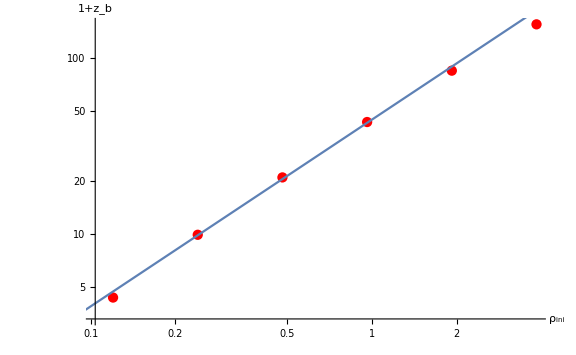

```mathematica
Show[A1 ,Plot[1.06x+3.8,{x,-7,20}]]
```